```mathematica
EntityProperties["AdministrativeDivision"]
```

{accommodation and food services sales,number of aggravated assaults,rate of aggravated assault,aggregate household income,annual births,annual deaths,housing units change rate,area,average ACT composite score,average ACT English score,average ACT math score,average ACT reading score,average ACT science score,average commute time,average home sale price,average SAT reading score,average SAT math score,average SAT writing score,average total SAT score,bordering counties,bordering states,number of burglaries,rate of burglary,number of businesses,business ownership by ethnicity,Amerindian business ownership fraction,Asian business ownership fraction,black business ownership fraction,Hispanic business ownership fraction,Pacific Islander business ownership fraction,white business ownership fraction,business ownership by gender,capital city,capital name,civilian labor force,civilian unemployment rate,coincident economic activity index,coordinates,country,county sales tax rate,total rate of crime,total number of crimes,disabled people,district court,earnings,average earnings per job,employment,employment change,farmland area,federal government expenditure,federal government expenditure per capita,FIPS code,flag,number of rapes,rate of rape,fraction foreign born,high school graduates taking ACT,high school graduates taking SAT,Gini index,government employment,GDP,GSP,has polygon?,insured population fraction,people with health insurance,people without health insurance,uninsured population fraction,highest elevation,highest point,highest sales tax rate,home ownership rate,home vacancy rate,house price index,housing permits,housing starts,households,housing units change,housing in multiple unit structures,infant deaths,land area,number of larcenies,rate of larceny,latitude,longitude,lowest elevation,lowest point,lowest sales tax rate,manufacturing value of shipments,mean elevation,median age,median household income,median home sale price,median total sales tax rate,minimum wage,number of motor vehicle thefts,rate of motor vehicle thefts,state mottoes,incidents of murder and nonnegligent manslaughter,rate of murder and nonnegligent manslaughter,name,new housing units,new housing units value,state nicknames,nonemployer businesses,median owner-occupied home value,owner-occupied housing,parent region,per capita income,per capita personal income,people per household,polygon,population,population by educational attainment,population by migration in previous 12 months,population by language spoken at home,population by marital status,population by poverty status,population by school enrollment,population density,position,private non-farm employment,private non-farm employment change,private non-farm businesses,total rate of property crime,total number of property crimes,residential rental vacancy rate,4 bedroom apartment fair market rent,1 bedroom apartment fair market rent,3 bedroom apartment fair market rent,2 bedroom apartment fair market rent,studio apartment fair market rent,retail sales,retail sales per capita,number of robberies,rate of robbery,state slogan,state song,abbreviation,state government tax collections,state sales tax rate,subdivisions,time zones,total voter registration rate,total voting rate,state tree,unweighted sample housing units,unweighted sample population,total rate of violent crime,total number of violent crimes,wholesale sales,employment,ZIP codes}

```mathematica
category = Select[EntityProperties["AdministrativeDivision"],StringContainsQ[CanonicalName[#], "BusinessGenderOwnershipFractions"]&][[1]]
```

business ownership by gender

```mathematica
usstates=EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]];
```

```mathematica
EntityProperties["AdministrativeDivision"]
```

```mathematica
EntityValue[category[[1]],"Definition"]
```

Missing[NotAvailable]

```mathematica
value=EntityValue[usstates,category][[All,1,2]]
```

{28.1 %,28.1 %,24.5 %,30.3 %,29.2 %,28.1 %,26.1 %,28.9 %,30.9 %,23.5 %,30.5 %,26.8 %,25.5 %,27.5 %,25.6 %,27.4 %,25.6 %,32.6 %,29.8 %,30.4 %,26.8 %,26.9 %,26.1 %,24.6 %,25.7 %,28.6 %,25.8 %,27.3 %,31.7 %,30.4 %,28.2 %,24.8 %,27.7 %,25.3 %,29.8 %,27. %,27.3 %,27.6 %,22.2 %,25.9 %,28.2 %,24.9 %,26. %,30.1 %,28.7 %,28.1 %,25.9 %,25.5 %}

```mathematica
forplot=Table[usstates[[ii]]-> value[[ii]],{ii,Length[usstates]}];
```

```mathematica
EntityValue[usstates,category][[All,1,2]]
```

{28.1 %,28.1 %,24.5 %,30.3 %,29.2 %,28.1 %,26.1 %,28.9 %,30.9 %,23.5 %,30.5 %,26.8 %,25.5 %,27.5 %,25.6 %,27.4 %,25.6 %,32.6 %,29.8 %,30.4 %,26.8 %,26.9 %,26.1 %,24.6 %,25.7 %,28.6 %,25.8 %,27.3 %,31.7 %,30.4 %,28.2 %,24.8 %,27.7 %,25.3 %,29.8 %,27. %,27.3 %,27.6 %,22.2 %,25.9 %,28.2 %,24.9 %,26. %,30.1 %,28.7 %,28.1 %,25.9 %,25.5 %}

```mathematica
GeoRegionValuePlot[forplot]
```

-Graphics-

```mathematica
category2=Select[EntityProperties["AdministrativeDivision"],StringContainsQ[CanonicalName[#], "Educational"]&][[1]]
```

population by educational attainment

```mathematica
GeoRegionValuePlot[usstates->category2,ColorFunctionScaling->True]
```

-Graphics-

```mathematica
(* 
annual births-deaths-population - health insurance - "civilian unemployment rate", employment - "uninsured population fraction" "people with/out health insurance "home ownership rate""   "home vacancy rate"
"infant deaths" "minimum wage" "per capita income" "population by poverty status" "population density" "position"
*)
```

```mathematica
(* annual deaths / population = % of people per state who die every year *)
```

```mathematica
(* people without health insurance / population = % of people who do not have health insurance *)
```

```mathematica
(* other stuff that may be interesting from the above list *)
```

```mathematica
(* Preliminary for CE: *)
```

```mathematica
populationentity = Select[EntityProperties["AdministrativeDivision"],StringContainsQ[CanonicalName[#], "Population"]&][[1]]
```

population

```mathematica
populationvalue = value=EntityValue[usstates,populationentity];
```

```mathematica
deathsentity=  Select[EntityProperties["AdministrativeDivision"],StringContainsQ[CanonicalName[#], "Deaths"]&][[1]]
```

annual deaths

```mathematica
deathsvalue = value=EntityValue[usstates,deathsentity];
```

```mathematica
nohientity = Select[EntityProperties["AdministrativeDivision"],StringContainsQ[CanonicalName[#], "Insurance"]&][[3]]
```

people without health insurance

```mathematica
nohivalue = value=EntityValue[usstates,nohientity];
```

```mathematica
toplot=Table[usstates[[ii]]-> deathsvalue[[ii]],{ii,Length[usstates]}];
```

```mathematica
GeoRegionValuePlot[Table[usstates[[ii]]-> deathsvalue[[ii]],{ii,Length[usstates]}]]
```

-Graphics-

```mathematica
GeoRegionValuePlot[Table[usstates[[ii]]-> nohivalue[[ii]],{ii,Length[usstates]}]]
```

-Graphics-

```mathematica
deathpercentage =deathsvalue/populationvalue ;
```

```mathematica
nohipercentage = nohivalue/populationvalue ;
```

```mathematica
correlation = deathpercentage/nohipercentage;
```

```mathematica
GeoRegionValuePlot[Table[usstates[[ii]]-> correlation[[ii]],{ii,Length[usstates]}]]
```

-Graphics-

```mathematica
Correlation[deathsvalue,nohivalue]
```

0.927885

```mathematica
deathsvaluenorm = Normalize[deathsvalue];
```

```mathematica
nohivaluenorm = Normalize[nohivalue];
```

```mathematica
forlistplot = Table[{deathsvaluenorm[[i]],nohivaluenorm[[i]]},{i,Length[deathsvaluenorm]}];
```

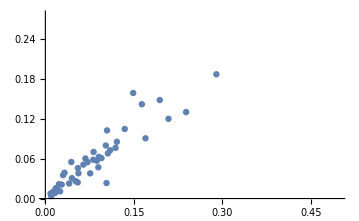

```mathematica
plt1 = ListPlot[forlistplot]
```

```mathematica
fitted = Fit[forlistplot, {1,x},x]
```

-0.0254008+1.07092 x

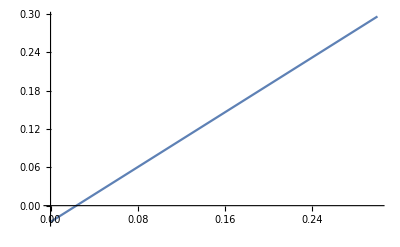

```mathematica
plt2= Plot[fitted,{x,0,0.3}]
```

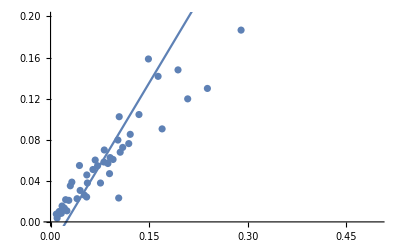

```mathematica
Show[plt1,plt2,PlotRange->{0,0.2}]
```

```mathematica
Select[EntityProperties["AdministrativeDivision"],StringContainsQ[CanonicalName[#], "Age"]&][[1]]
```

median age

```mathematica
(* Next: remove the clusster at the bottom, so the line is better fitted *)
```